## Setup

```mathematica
(* === SETUP === *)
SetDirectory[NotebookDirectory[]];
```

```mathematica
LaunchKernels[14];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\tests\\QKT_full.wl"];
```

```mathematica
(* === PARAMETERS (modify freely) === *)
J       = 500;
alpha   = Pi/2.;
kCenter = 8.5;
delta   = 0.001;
nQKT    = 100;
nCOE    = 50;
Lmax    = 20;
lDomain = Range[0.5, Lmax, 0.2];
```

```mathematica
kValues=RandomReal[{kCenter-delta,kCenter+delta},500];
```

## COE

```mathematica
(* ================================================================ *)
(* PART A: COE REFERENCE ENSEMBLE                                   *)
(* ================================================================ *)
dimCOE = J + 1;   (* single reference dimension *)
Print["Generating ", nCOE, " COE(", dimCOE, ") matrices..."];
AbsoluteTiming[coeSpectra = GenerateCOEEnsemble[dimCOE, nCOE];]
Print["Done. N = ", coeSpectra[[1]]["N"]];
```

Generating 50 COE(501) matrices...

{25.9522,Null}

Done. N = 501

```mathematica
(* --- A1. Unfolding validation --- *)
nR = Length[coeSpectra];
sampleIdx = Round[Subdivide[1, nR, 2]];
vdCOE = Map[ValidateUnfolding, coeSpectra[[sampleIdx]]];
```

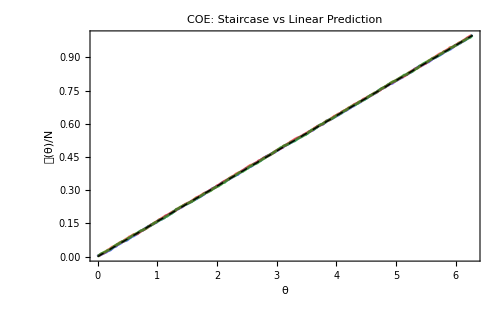

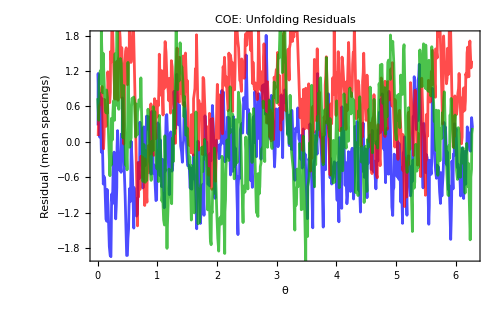

```mathematica
Show[
  Table[ListLinePlot[
    Transpose[{vdCOE[[i]]["Phases"], vdCOE[[i]]["EmpiricalCDF"]}],
    PlotStyle -> {{Blue, Red, Darker[Green]}[[i]], Opacity[0.6]}
  ], {i, 3}],
  Plot[x / (2 Pi), {x, 0, 2 Pi}, PlotStyle -> {Black, Dashed, Thick}],
  Frame -> True,
  FrameLabel -> {"θ", "𝒩(θ)/N"},
  PlotLabel -> "COE: Staircase vs Linear Prediction",
  ImageSize -> 500
]

Show[
  Table[ListLinePlot[
    Transpose[{vdCOE[[i]]["Phases"], vdCOE[[i]]["Residuals"]}],
    PlotStyle -> {{Blue, Red, Darker[Green]}[[i]], Opacity[0.7]}
  ], {i, 3}],
  Frame -> True,
  FrameLabel -> {"θ", "Residual (mean spacings)"},
  PlotLabel -> "COE: Unfolding Residuals",
  ImageSize -> 500
]
```

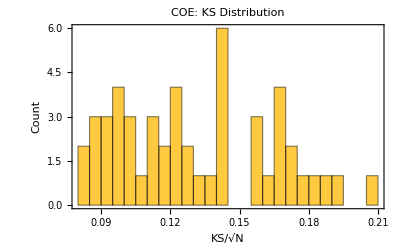

COE KS: mean = 0.1309, max = 0.2078

```mathematica
allKScoe = Map[ValidateUnfolding[#]["KS"] &, coeSpectra];
Histogram[allKScoe, 20, Frame -> True,
  FrameLabel -> {"KS/\!\(\*SqrtBox[\(N\)]\)", "Count"},
  PlotLabel -> "COE: KS Distribution", ImageSize -> 400]
Print["COE KS: mean = ", NumberForm[Mean[allKScoe], 4],
  ", max = ", NumberForm[Max[allKScoe], 4]];
```

```mathematica
(* --- A2. NNSD + cumulative --- *)
allSpacingsCOE = Sort[Flatten[Map[NNSpacings, coeSpectra]]];
nSpCOE = Length[allSpacingsCOE];
empCDFcoe = Range[nSpCOE] / nSpCOE;
```

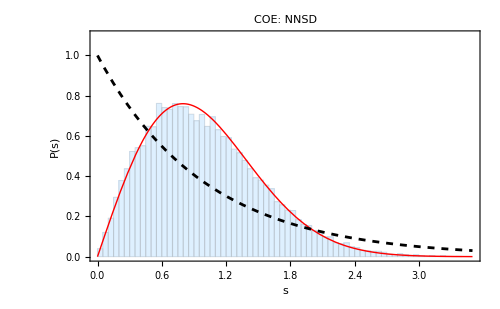

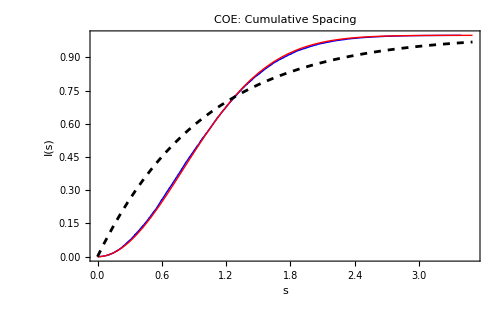

```mathematica
Show[
  Histogram[allSpacingsCOE, {0, 4, 0.05}, "ProbabilityDensity",
    ChartStyle -> Directive[LightBlue, EdgeForm[Gray]],
    PlotRange -> {{0, 3.5}, {0, 1.1}}],
  Plot[WignerCOE[s], {s, 0, 3.5}, PlotStyle -> {Red, Thick}],
  Plot[Exp[-s], {s, 0, 3.5}, PlotStyle -> {Black, Dashed}],
  Frame -> True, FrameLabel -> {"s", "P(s)"},
  PlotLabel -> "COE: NNSD", ImageSize -> 500]

Show[
  ListLinePlot[Transpose[{allSpacingsCOE, empCDFcoe}],
    PlotStyle -> {Blue, Thick}, PlotRange -> {{0, 3.5}, {0, 1}}],
  Plot[IntWignerCOE[s], {s, 0, 3.5}, PlotStyle -> {Red, Thick}],
  Plot[1 - Exp[-s], {s, 0, 3.5}, PlotStyle -> {Black, Dashed}],
  Frame -> True, FrameLabel -> {"s", "I(s)"},
  PlotLabel -> "COE: Cumulative Spacing", ImageSize -> 500]
```

```mathematica
coeCDFvals = Map[IntWignerCOE, allSpacingsCOE];
Print["COE <s> = ", NumberForm[Mean[allSpacingsCOE], 5]];
Print["COE Var(s) = ", NumberForm[Variance[allSpacingsCOE], 5],
  "  (COE surmise: ", NumberForm[N[4/Pi - 1], 4], ")"];
Print["COE KS(vs surmise) = ",
  NumberForm[Max[Abs[empCDFcoe - coeCDFvals]], 4]];
```

COE <s> = 1.

COE Var(s) = 0.28924  (COE surmise: 0.2732)

COE KS(vs surmise) = 0.0119

```mathematica
(* --- A3. Number variance --- *)
Print["\nComputing COE number variance..."];
AbsoluteTiming[sigma2COE = EnsembleSigma2[coeSpectra, lDomain];]
```

Computing COE number variance...

{9.08616,Null}

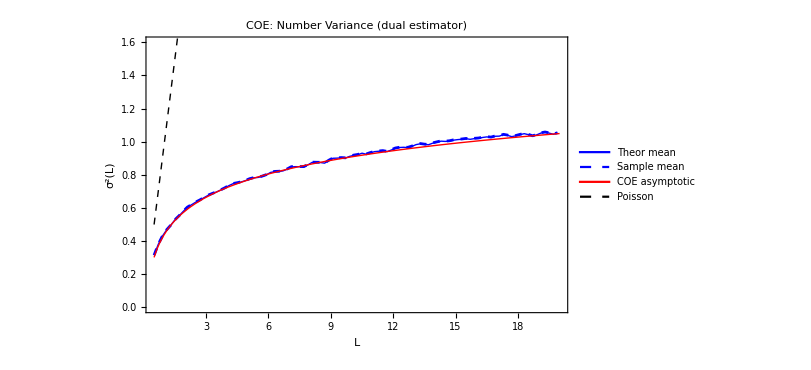

```mathematica
(* Dual estimator *)
Legended[
  Show[
    ListLinePlot[
      {Transpose[{sigma2COE["LValues"], sigma2COE["Sigma2TheorMean"]}],
       Transpose[{sigma2COE["LValues"], sigma2COE["Sigma2SampleMean"]}]},
      PlotStyle -> {{Blue, Thick}, {Blue, Dashed}}, PlotRange -> All],
    Plot[COEAsymptoticSigma2[L], {L, 0.5, Lmax},
      PlotStyle -> {Red, Thick}],
    Plot[L, {L, 0.5, Lmax}, PlotStyle -> {Black, Dashed, Thin}],
    Frame -> True,
    FrameLabel -> {"L", "\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},
    PlotLabel -> "COE: Number Variance (dual estimator)",
    ImageSize -> 600,
PlotRange->{All,{0,1.6}}
  ],
  Placed[LineLegend[
    {Directive[Blue, Thick], Directive[Blue, Dashed],
     Directive[Red, Thick], Directive[Black, Dashed, Thin]},
    {"Theor mean", "Sample mean", "COE asymptotic", "Poisson"},
    LabelStyle -> Directive[Black, 12]
  ], {Right, Bottom}]
]
```

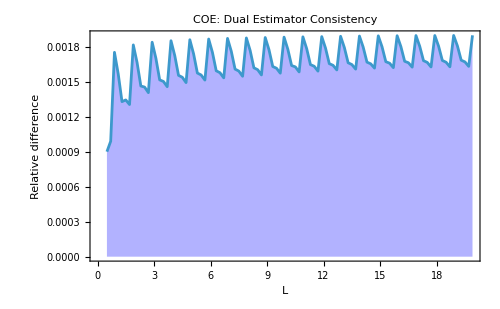

COE max rel diff = 0.001899

```mathematica
relDiffCOE = Abs[sigma2COE["Sigma2TheorMean"] - sigma2COE["Sigma2SampleMean"]] /
  (sigma2COE["Sigma2TheorMean"] + 10^-10);
ListLinePlot[Transpose[{sigma2COE["LValues"], relDiffCOE}],
  Filling -> Axis, FillingStyle -> Directive[Opacity[0.3], Blue],
  Frame -> True, PlotRange -> {0, All},
  FrameLabel -> {"L", "Relative difference"},
  PlotLabel -> "COE: Dual Estimator Consistency", ImageSize -> 500]
Print["COE max rel diff = ", NumberForm[Max[relDiffCOE], 4]];
```

## QKT

```mathematica
?ClassicalMapeo
```

```mathematica
(*Quick Poincaré section*)
pts=ClassicalMapeo[{0.5,0.5},alpha,kCenter,100000,0];
ListPlot[pts,PlotStyle->{Black,PointSize[Tiny]},AspectRatio->1,PlotRange->{{-2,2},{-2,2}},Frame->True,PlotLabel->"Phase space k = "<>ToString[kCenter]]
```

```mathematica
(* ================================================================ *)
(* PART B: QKT ENSEMBLE                                             *)
(* ================================================================ *)

SeedRandom[123];
kList = RandomReal[{kCenter - delta, kCenter + delta}, nQKT];
Print["\nDiagonalizing ", nQKT, " QKT matrices (J=", J, ")..."];
AbsoluteTiming[qktEnsemble = GenerateQKTEnsemble[J, alpha, kList];]
Print["Even N = ", qktEnsemble["Even"][[1]]["N"],
  ", Odd N = ", qktEnsemble["Odd"][[1]]["N"]];
```

Diagonalizing 100 QKT matrices (J=500)...

{267.04,Null}

Even N = 501, Odd N = 500

```mathematica
dataeven=Import["C:\\Users\\Miguel\\Desktop\\plots_J_1000\\spectra_k25.0_even.mx"];
dataodd=Import["C:\\Users\\Miguel\\Desktop\\plots_J_1000\\spectra_k25.0.mx"];
```

```mathematica
qktEnsemble=<|"Even"->dataeven,"Odd"->dataodd|>;
```

--- QKT Even sector ---

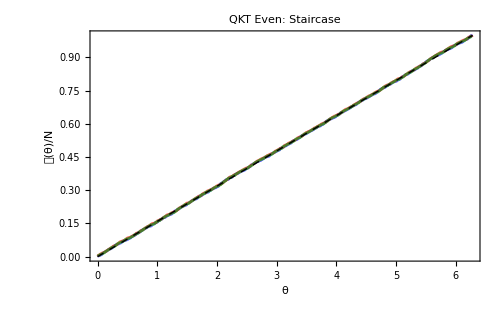

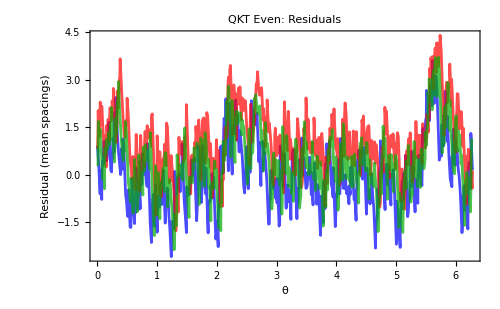

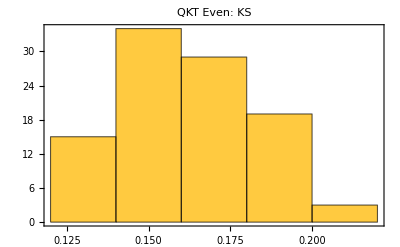

KS: mean = 0.1623, max = 0.2138

--- QKT Odd sector ---

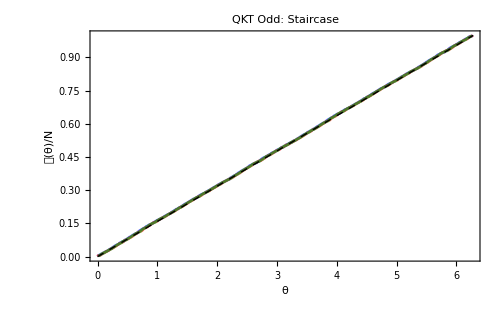

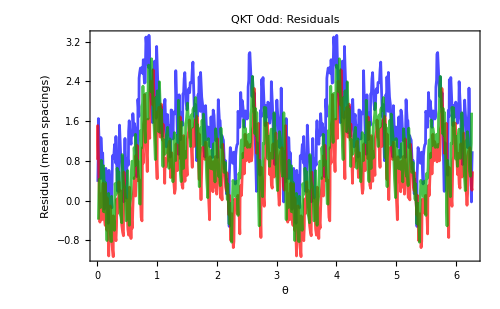

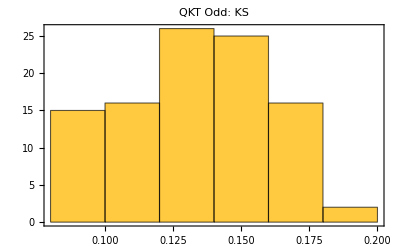

KS: mean = 0.1334, max = 0.1897

```mathematica
(* --- B1. Unfolding validation per sector --- *)
Do[
  specList = qktEnsemble[sec];
  nR = Length[specList];
  sIdx = Round[Subdivide[1, nR, 2]];
  vd = Map[ValidateUnfolding, specList[[sIdx]]];

  Print["\n--- QKT ", sec, " sector ---"];
  Print[Show[
    Table[ListLinePlot[
      Transpose[{vd[[i]]["Phases"], vd[[i]]["EmpiricalCDF"]}],
      PlotStyle -> {{Blue, Red, Darker[Green]}[[i]], Opacity[0.6]}
    ], {i, 3}],
    Plot[x / (2 Pi), {x, 0, 2 Pi}, PlotStyle -> {Black, Dashed, Thick}],
    Frame -> True,
    FrameLabel -> {"θ", "𝒩(θ)/N"},
    PlotLabel -> "QKT " <> sec <> ": Staircase", ImageSize -> 500]];

  Print[Show[
    Table[ListLinePlot[
      Transpose[{vd[[i]]["Phases"], vd[[i]]["Residuals"]}],
      PlotStyle -> {{Blue, Red, Darker[Green]}[[i]], Opacity[0.7]}
    ], {i, 3}],
    Frame -> True,
    FrameLabel -> {"θ", "Residual (mean spacings)"},
    PlotLabel -> "QKT " <> sec <> ": Residuals",PlotRange->All, ImageSize -> 500]];

  ksV = Map[ValidateUnfolding[#]["KS"] &, specList];
  Print[Histogram[ksV, Automatic, Frame -> True,
    PlotLabel -> "QKT " <> sec <> ": KS", ImageSize -> 400]];
  Print["KS: mean = ", NumberForm[Mean[ksV], 4],
    ", max = ", NumberForm[Max[ksV], 4]];
, {sec, {"Even", "Odd"}}];
```

--- QKT Even: NNSD ---

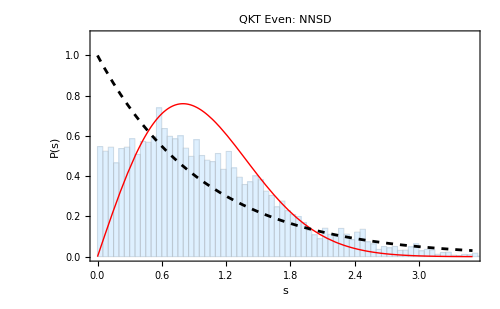

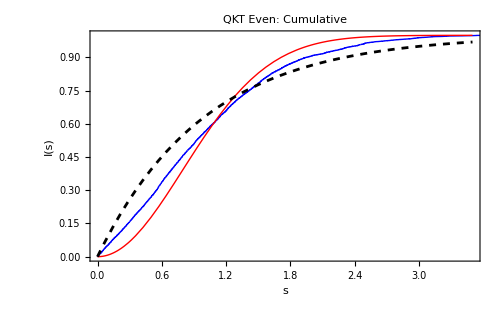

--- QKT Odd: NNSD ---

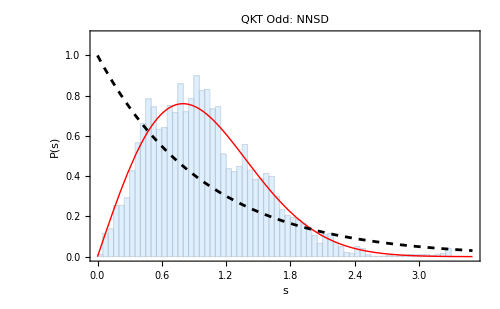

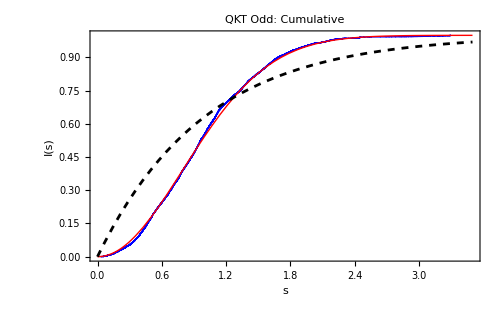

```mathematica
(* --- B2. NNSD + cumulative per sector --- *)
Do[
  specList = qktEnsemble[sec];
  spacings = Sort[Flatten[Map[NNSpacings, specList]]];
  nSp = Length[spacings];
empCDF = Range[nSp] / nSp;

  Print["\n--- QKT ", sec, ": NNSD ---"];
  Print[Show[
    Histogram[spacings, {0, 4, 0.05}, "ProbabilityDensity",
      ChartStyle -> Directive[LightBlue, EdgeForm[Gray]],
      PlotRange -> {{0, 3.5}, {0, 1.1}}],
    Plot[WignerCOE[s], {s, 0, 3.5}, PlotStyle -> {Red, Thick}],
    Plot[Exp[-s], {s, 0, 3.5}, PlotStyle -> {Black, Dashed}],
    Frame -> True, FrameLabel -> {"s", "P(s)"},
    PlotLabel -> "QKT " <> sec <> ": NNSD", ImageSize -> 500]];

  Print[Show[
    ListLinePlot[Transpose[{spacings, empCDF}],
      PlotStyle -> {Blue, Thick}, PlotRange -> {{0, 3.5}, {0, 1}}],
    Plot[IntWignerCOE[s], {s, 0, 3.5}, PlotStyle -> {Red, Thick}],
    Plot[1 - Exp[-s], {s, 0, 3.5}, PlotStyle -> {Black, Dashed}],
    Frame -> True, FrameLabel -> {"s", "I(s)"},
    PlotLabel -> "QKT " <> sec <> ": Cumulative", ImageSize -> 500]];

, {sec, {"Even", "Odd"}}];
```

```mathematica
(* --- B2. NNSD + cumulative per sector --- *)
Do[
  specList = qktEnsemble[sec];
  spacings = Sort[Flatten[Map[NNSpacings, specList]]];
  nSp = Length[spacings];
empCDF = Range[nSp] / nSp;

cdfAt =Map[IntWignerCOE, spacings];
  Print["<s> = ", NumberForm[Mean[spacings], 5]];
  Print["Var(s) = ", NumberForm[Variance[spacings], 5],
    "  (COE: ", NumberForm[N[4/Pi - 1], 4], ")"];
  Print["KS(vs COE) = ", NumberForm[Max[Abs[empCDF - cdfAt]], 4]];

, {sec, {"Even", "Odd"}}];
```

<s> = 1.

Var(s) = 0.4844  (COE: 0.2732)

KS(vs COE) = 0.09626

<s> = 1.

Var(s) = 0.27113  (COE: 0.2732)

KS(vs COE) = 0.02553

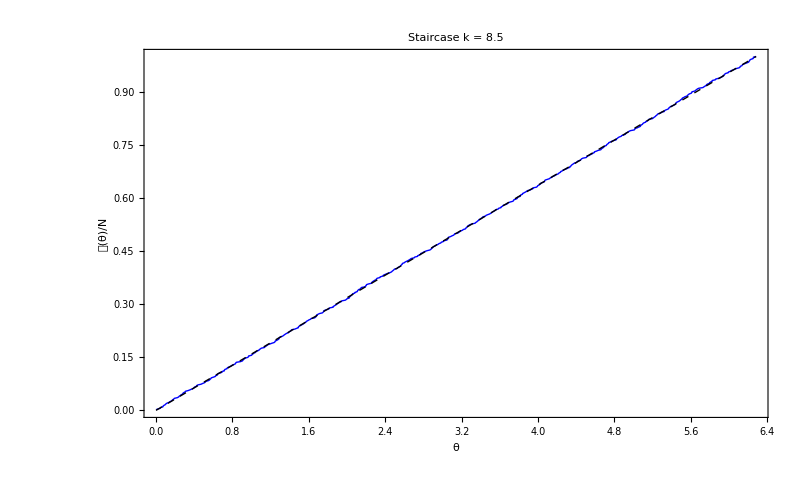

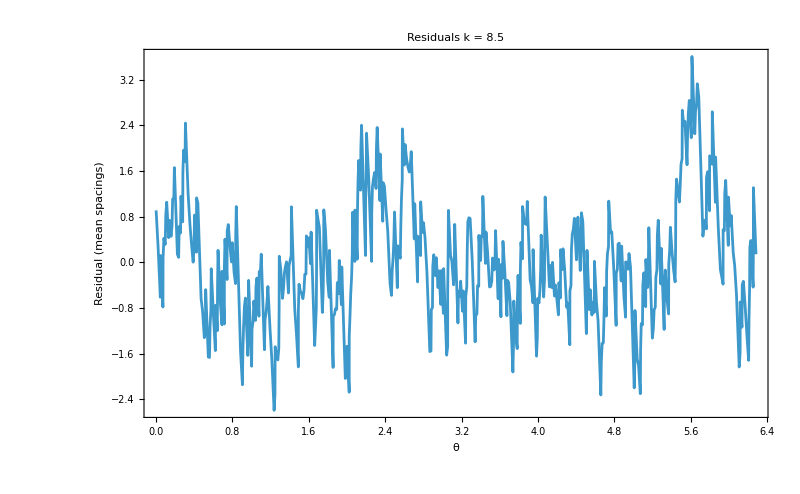

KS = 0.1611

```mathematica
vd=ValidateUnfolding[qktEnsemble["Even"][[1]]];

Show[ListLinePlot[Transpose[{vd["Phases"],vd["EmpiricalCDF"]}],PlotStyle->{Blue,Thick}],Plot[x/(2 Pi),{x,0,2 Pi},PlotStyle->{Black,Dashed,Thick}],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"θ","𝒩(θ)/N"},PlotLabel->"Staircase k = "<>ToString[kCenter]]

ListLinePlot[Transpose[{vd["Phases"],vd["Residuals"]}],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"θ","Residual (mean spacings)"},PlotLabel->"Residuals k = "<>ToString[kCenter]]

Print["KS = ",NumberForm[vd["KS"],4]];
```

```mathematica
(*Pool ALL 20 vs single realization*)
spacingsAll=Sort[Flatten[Map[NNSpacings,qktEnsemble["Even"]]]];
spacingsOne=NNSpacings[qktEnsemble["Even"][[1]]];

Print["Pooled: n=",Length[spacingsAll],", <s>=",NumberForm[Mean[spacingsAll],5],", Var=",NumberForm[Variance[spacingsAll],5]];
Print["Single: n=",Length[spacingsOne],", <s>=",NumberForm[Mean[spacingsOne],5],", Var=",NumberForm[Variance[spacingsOne],5]];
Print["COE Var = ",NumberForm[N[4/Pi-1],5]];
```

Pooled: n=50100, <s>=1., Var=0.4844

Single: n=501, <s>=1., Var=0.48441

COE Var = 0.27324

```mathematica
allR=Table[sp=NNSpacings[qktEnsemble["Odd"][[i]]];
ratios=Min/@Transpose[{Most[sp]/Rest[sp],Rest[sp]/Most[sp]}];
Mean[ratios],{i,Length[qktEnsemble["Odd"]]}];
Print["<r> per realization: ",NumberForm[Mean[allR],5]," +/- ",NumberForm[StandardDeviation[allR],4]];
```

<r> per realization: 0.54684 +/- 0.01193

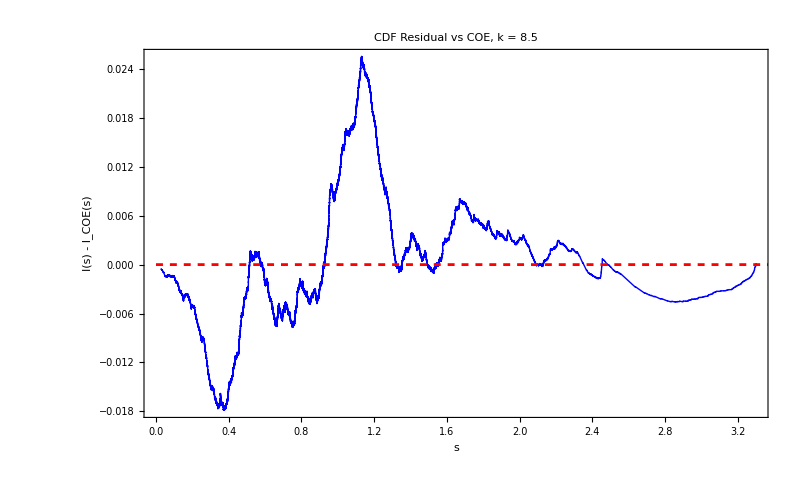

Max |I - I_COE| = 0.0255259

```mathematica
(*Pool spacings*)
spacingsAll=Sort[Flatten[Map[NNSpacings,qktEnsemble["Odd"]]]];
nSp=Length[spacingsAll];
empCDF=Range[nSp]/nSp;
coeCDF=Map[IntWignerCOE,spacingsAll];

(*Difference:amplifies small deviations*)
Show[ListLinePlot[Transpose[{spacingsAll,empCDF-coeCDF}],PlotStyle->{Blue,Thick}],Plot[0,{x,0,4},PlotStyle->{Red,Dashed}],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"s","I(s) - I_COE(s)"},PlotLabel->"CDF Residual vs COE, k = "<>ToString[kCenter]]

Print["Max |I - I_COE| = ",Max[Abs[empCDF-coeCDF]]];
```

```mathematica
(* ===Spacing ratio distribution P(r)===*)(*Analytical predictions (Atas et al.2013)*)
PrCOE[r_]:=(27/4) (r+r^2)/(1+r+r^2)^(5/2);
PrCUE[r_]:=(81 Sqrt[3]/(4 Pi)) (r+r^2)^2/(1+r+r^2)^4;
PrPoisson[r_]:=2/(1+r)^2;
```

```mathematica
(*Compute r=min(s_i,s_{i+1})/max(s_i,s_{i+1}) for all realizations*)
allRatios=Flatten[Table[sp=Differences[qktEnsemble["Even"][[i]]["Spectrum"]];
Min/@Transpose[{Most[sp]/Rest[sp],Rest[sp]/Most[sp]}],{i,Length[qktEnsemble["Even"]]}]];

Print["<r> = ",NumberForm[Mean[allRatios],5],"  (COE: 0.5359, CUE: 0.6027, Poisson: 0.3863)"];
```

<r> = 0.42295  (COE: 0.5359, CUE: 0.6027, Poisson: 0.3863)

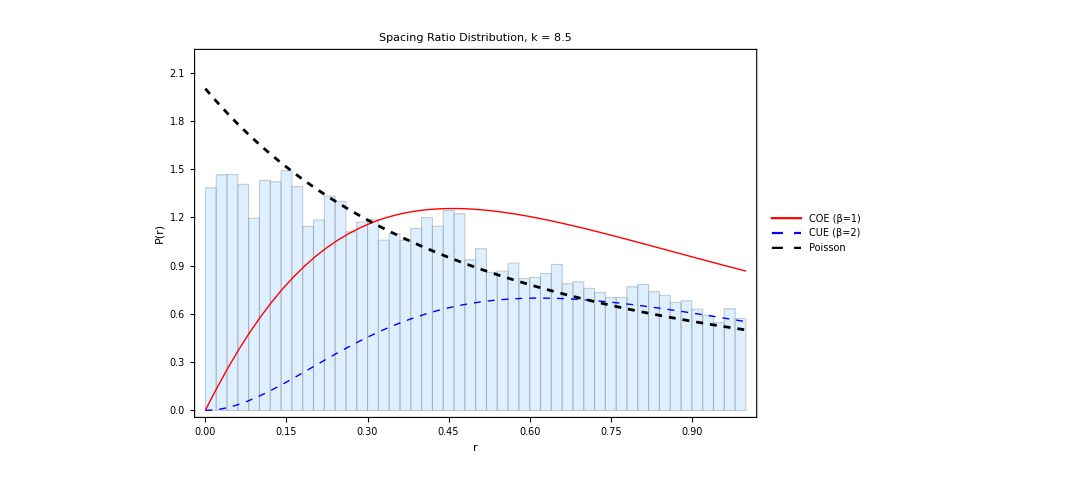

```mathematica
(*Histogram+predictions*)
Legended[Show[Histogram[allRatios,{0,1,0.02},"ProbabilityDensity",ChartStyle->Directive[LightBlue,EdgeForm[Gray]],PlotRange->{{0,1},{0,2.2}}],Plot[PrCOE[r],{r,0,1},PlotStyle->{Red,Thick}],Plot[PrCUE[r],{r,0,1},PlotStyle->{Blue,Thick,Dashed}],Plot[PrPoisson[r],{r,0,1},PlotStyle->{Black,Dashed}],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"r","P(r)"},PlotLabel->"Spacing Ratio Distribution, k = "<>ToString[kCenter]],Placed[LineLegend[{Directive[Red,Thick],Directive[Blue,Thick,Dashed],Directive[Black,Dashed]},{"COE (β=1)","CUE (β=2)","Poisson"},LabelStyle->Directive[Black,18]],{Right,Bottom}]]
```

```mathematica
(*Also cumulative—binning-free*)
sortedR=Sort[allRatios];
nR=Length[sortedR];
empCDFr=Range[nR]/nR;
intCOE=Table[NIntegrate[PrCOE[r],{r,0,x}],{x,sortedR}];
```

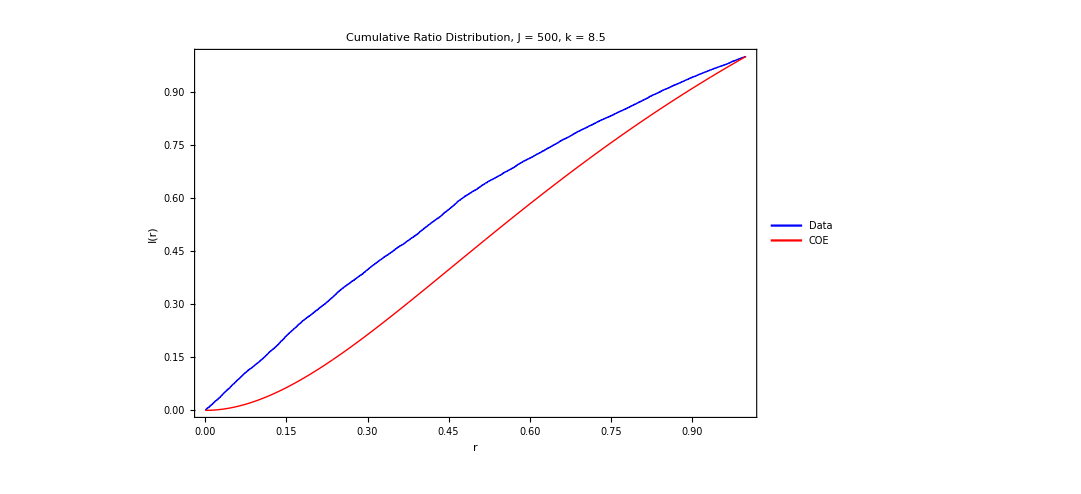

KS(r vs COE) = 0.184441

```mathematica
Legended[Show[ListLinePlot[Transpose[{sortedR,empCDFr}],PlotStyle->{Blue,Thick},PlotRange->{{0,1},{0,1}}],ListLinePlot[Transpose[{sortedR,intCOE}],PlotStyle->{Red,Thick}],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"r","I(r)"},PlotLabel->"Cumulative Ratio Distribution, J = 500, k = "<>ToString[kCenter]],Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick]},{"Data","COE"},LabelStyle->Directive[Black,18]],{Right,Bottom}]]

Print["KS(r vs COE) = ",Max[Abs[empCDFr-intCOE]]];
```

# Number variance

```mathematica
(* --- B3. Number variance per sector --- *)
Print["\nComputing QKT number variance..."];
AbsoluteTiming[sigma2Even = EnsembleSigma2[qktEnsemble["Even"], lDomain];]
AbsoluteTiming[sigma2Odd  = EnsembleSigma2[qktEnsemble["Odd"], lDomain];]
```

Computing QKT number variance...

{40.0584,Null}

{38.3107,Null}

```mathematica
(* Dual estimator per sector *)
Do[
  s2 = If[sec == "Even", sigma2Even, sigma2Odd];
  rd = Abs[s2["Sigma2TheorMean"] - s2["Sigma2SampleMean"]] /
    (s2["Sigma2TheorMean"] + 10^-10);
  Print["\n--- QKT ", sec, " dual estimator ---"];
  Print[ListLinePlot[Transpose[{s2["LValues"], rd}],
    Filling -> Axis, FillingStyle -> Directive[Opacity[0.3], Blue],
    Frame -> True, PlotRange -> {0, All},
    FrameLabel -> {"L", "Rel diff"},
    PlotLabel -> "QKT " <> sec <> ": Dual Estimator", ImageSize -> 500]];
  Print["Max rel diff = ", NumberForm[Max[rd], 4]];
, {sec, {"Even", "Odd"}}];
```

--- QKT Even dual estimator ---

Max rel diff = 0.001854

--- QKT Odd dual estimator ---

Max rel diff = 0.00186

## Comparison

```mathematica
(* ================================================================ *)
(* PART C: FINAL COMPARISON                                         *)
(* ================================================================ *)

Print["\n=== FINAL COMPARISON ==="];

lCOE  = sigma2COE["LValues"];
lEven = sigma2Even["LValues"];
lOdd  = sigma2Odd["LValues"];

dimE = qktEnsemble["Even"][[1]]["N"];
dimO = qktEnsemble["Odd"][[1]]["N"];

(* --- C1. All curves on one plot --- *)
Legended[
  Show[
    (* COE error band *)
    ListLinePlot[
      {Transpose[{lCOE, sigma2COE["Sigma2TheorMean"] + sigma2COE["SETheorMean"]}],
       Transpose[{lCOE, sigma2COE["Sigma2TheorMean"] - sigma2COE["SETheorMean"]}]},
      PlotStyle -> None, Filling -> {1 -> {2}},
      FillingStyle -> Directive[Opacity[0.15], Red]],
    ListLinePlot[Transpose[{lCOE, sigma2COE["Sigma2TheorMean"]}],
      PlotStyle -> {Red, Thick}],
    (* Even QKT *)
    ListLinePlot[
      {Transpose[{lEven, sigma2Even["Sigma2TheorMean"] + sigma2Even["SETheorMean"]}],
       Transpose[{lEven, sigma2Even["Sigma2TheorMean"] - sigma2Even["SETheorMean"]}]},
      PlotStyle -> None, Filling -> {1 -> {2}},
      FillingStyle -> Directive[Opacity[0.15], Blue]],
    ListLinePlot[Transpose[{lEven, sigma2Even["Sigma2TheorMean"]}],
      PlotStyle -> {Blue, Thick}],
    (* Odd QKT *)
    ListLinePlot[
      {Transpose[{lOdd, sigma2Odd["Sigma2TheorMean"] + sigma2Odd["SETheorMean"]}],
       Transpose[{lOdd, sigma2Odd["Sigma2TheorMean"] - sigma2Odd["SETheorMean"]}]},
      PlotStyle -> None, Filling -> {1 -> {2}},
      FillingStyle -> Directive[Opacity[0.15], Darker[Green]]],
    ListLinePlot[Transpose[{lOdd, sigma2Odd["Sigma2TheorMean"]}],
      PlotStyle -> {Darker[Green], Thick}],
    (* Asymptotic + Poisson *)
    Plot[COEAsymptoticSigma2[L], {L, 0.5, Lmax},
      PlotStyle -> {Orange, Thick, Dashed}],
    Plot[L, {L, 0.5, Lmax}, PlotStyle -> {Black, Dashed, Thin}],
    Frame -> True,
    FrameLabel -> {"L", "\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},
    FrameStyle -> Directive[Black, 20],
    LabelStyle -> Directive[Black, 16],
    PlotLabel -> "Number Variance: QKT vs COE(" <> ToString[dimCOE] <> ")",
    PlotRange -> {All, {0, Automatic}},
    ImageSize -> 700
  ],
  Placed[LineLegend[
    {Directive[Blue, Thick], Directive[Darker[Green], Thick],
     Directive[Red, Thick], Directive[Orange, Thick, Dashed],
     Directive[Black, Dashed, Thin]},
    {"QKT Even (N=" <> ToString[dimE] <> ")",
     "QKT Odd (N=" <> ToString[dimO] <> ")",
     "COE(N=" <> ToString[dimCOE] <> ")",
     "COE asymptotic", "Poisson"},
    LabelStyle -> Directive[Black, 13]
  ], {Right, Top}]
]
```

=== FINAL COMPARISON ===

```mathematica
(* --- C2. Residuals vs COE --- *)
nMinL = Min[Length[lCOE], Length[lEven], Length[lOdd]];
lRes = lCOE[[1 ;; nMinL]];

residualEven = sigma2Even["Sigma2TheorMean"][[1 ;; nMinL]] -
  sigma2COE["Sigma2TheorMean"][[1 ;; nMinL]];
residualOdd = sigma2Odd["Sigma2TheorMean"][[1 ;; nMinL]] -
  sigma2COE["Sigma2TheorMean"][[1 ;; nMinL]];
seResEven = Sqrt[sigma2Even["SETheorMean"][[1 ;; nMinL]]^2 +
  sigma2COE["SETheorMean"][[1 ;; nMinL]]^2];
seResOdd = Sqrt[sigma2Odd["SETheorMean"][[1 ;; nMinL]]^2 +
  sigma2COE["SETheorMean"][[1 ;; nMinL]]^2];

Legended[
  Show[
    ListLinePlot[
      {Transpose[{lRes, residualEven + seResEven}],
       Transpose[{lRes, residualEven - seResEven}]},
      PlotStyle -> None, Filling -> {1 -> {2}},
      FillingStyle -> Directive[Opacity[0.2], Blue]],
    ListLinePlot[Transpose[{lRes, residualEven}],
      PlotStyle -> {Blue, Thick}],
    ListLinePlot[
      {Transpose[{lRes, residualOdd + seResOdd}],
       Transpose[{lRes, residualOdd - seResOdd}]},
      PlotStyle -> None, Filling -> {1 -> {2}},
      FillingStyle -> Directive[Opacity[0.2], Darker[Green]]],
    ListLinePlot[Transpose[{lRes, residualOdd}],
      PlotStyle -> {Darker[Green], Thick}],
    Plot[0, {x, 0, Max[lRes]}, PlotStyle -> {Red, Dashed}],
    Frame -> True,
    FrameLabel -> {"L",
      "\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(QKT) - \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(COE)"},
    FrameStyle -> Directive[Black, 20],
    LabelStyle -> Directive[Black, 16],
    PlotLabel -> "Deviation from COE",
    ImageSize -> 600,
PlotRange->All
  ],
  Placed[LineLegend[
    {Directive[Blue, Thick], Directive[Darker[Green], Thick]},
    {"Even - COE", "Odd - COE"},
    LabelStyle -> Directive[Black, 14]
  ], {Right, Top}]
]
```

```mathematica
(* --- C3. Parity-averaged residual --- *)
avgSigma2 = (dimE * sigma2Even["Sigma2TheorMean"][[1 ;; nMinL]] +
             dimO * sigma2Odd["Sigma2TheorMean"][[1 ;; nMinL]]) / (dimE + dimO);
residualAvg = avgSigma2 - sigma2COE["Sigma2TheorMean"][[1 ;; nMinL]];

Legended[
  Show[
    ListLinePlot[Transpose[{lRes, residualAvg}],
      PlotStyle -> {Purple, Thick},
      Filling -> Axis, FillingStyle -> Directive[Opacity[0.2], Purple]],
    ListLinePlot[Transpose[{lRes, residualEven}],
      PlotStyle -> {Blue, Thin, Opacity[0.5]}],
    ListLinePlot[Transpose[{lRes, residualOdd}],
      PlotStyle -> {Darker[Green], Thin, Opacity[0.5]}],
    Plot[0, {x, 0, Max[lRes]}, PlotStyle -> {Red, Dashed}],
    Frame -> True,
    FrameLabel -> {"L",
      "\!\(\*SuperscriptBox[\(σ\), \(2\)]\) - \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(COE)"},
    FrameStyle -> Directive[Black, 20],
    LabelStyle -> Directive[Black, 16],
    PlotLabel -> "Parity-Averaged Residual vs COE",
    ImageSize -> 600
  ],
  Placed[LineLegend[
    {Directive[Purple, Thick], Directive[Blue, Thin, Opacity[0.5]],
     Directive[Darker[Green], Thin, Opacity[0.5]]},
    {"Weighted avg", "Even", "Odd"},
    LabelStyle -> Directive[Black, 14]
  ], {Right, Top}]
]

Print["\nDimension Even = ", dimE, ", Odd = ", dimO, ", COE = ", dimCOE];
Print["Max |avg residual| = ", NumberForm[Max[Abs[residualAvg]], 4]];
```

Dimension Even = 501, Odd = 500, COE = 501

Max |avg residual| = 0.05139

```mathematica
(* === SUMMARY === *)
Print["\n=== SUMMARY ==="];
Print["J = ", J, ", alpha = ", alpha, ", k ~ ", kCenter, " +/- ", delta];
Print["QKT realizations = ", nQKT, ", COE realizations = ", nCOE];
Print["Even N = ", dimE, ", Odd N = ", dimO, ", COE N = ", dimCOE];
Print["L range = [", lDomain[[1]], ", ", lDomain[[-1]], "]"];
Print["L/N max (even) ~ ", NumberForm[N[lDomain[[-1]] / dimE], 3]];
Print["L/N max (odd) ~ ", NumberForm[N[lDomain[[-1]] / dimO], 3]];
```

=== SUMMARY ===

J = 500, alpha = 0.84, k ~ 20. +/- 0.001

QKT realizations = 200, COE realizations = 40

Even N = 501, Odd N = 500, COE N = 501

L range = [0.5, 19.9]

L/N max (even) ~ 0.0397

L/N max (odd) ~ 0.0398

# SFF

## test 2

```mathematica
(* ==============================================================*)(*SFF:QKT ENSEMBLE+SINGLE REALIZATION vs COE ENSEMBLE*)(* ==============================================================*)COESFFAnalytical[tau_]:=Piecewise[{{2 tau-tau Log[1+2 tau],0<tau<1},{2-tau Log[(2 tau+1)/(2 tau-1)],tau>=1}}];

SingleSFF[specData_Association,tauMax_Real,nPts_Integer]:=Module[{taus},taus=N[Range[1,nPts] (tauMax/nPts)];
<|"Tau"->taus,"K"->CompileSFF[specData["Spectrum"],taus]|>];

EnsembleSFF[spectraList_List,tauMax_Real,nPts_Integer]:=Module[{nMat,taus,specArray,allK,meanK,seK},nMat=Length[spectraList];
taus=N[Range[1,nPts] (tauMax/nPts)];
specArray=Map[#["Spectrum"]&,spectraList];
DistributeDefinitions[CompileSFF,taus,specArray];
allK=ParallelTable[CompileSFF[specArray[[i]],taus],{i,nMat},Method->"CoarsestGrained"];
meanK=Mean[allK];
seK=StandardDeviation[allK]/Sqrt[nMat*1.0];
<|"Tau"->taus,"MeanK"->meanK,"SE"->seK|>];
```

```mathematica
(* ===Parameters===*)
J=500;
alpha=0.84;
k=15.;
nCOE=50;
nQKT=50;
delta=0.01;
tauMax=3.0;
nPts=1000;
```

```mathematica
(* ===QKT ensemble===*)
SeedRandom[42];
kList=RandomReal[{k-delta,k+delta},nQKT];
Print["Generating QKT ensemble..."];
qktEnsemble=GenerateQKTEnsemble[J,alpha,kList];
Print["Computing QKT ensemble SFF..."];
sffEvenEns=EnsembleSFF[qktEnsemble["Even"],tauMax,nPts];
sffOddEns=EnsembleSFF[qktEnsemble["Odd"],tauMax,nPts];
```

Generating QKT ensemble...

Computing QKT ensemble SFF...

```mathematica
(* ===COE ensemble===*)
dimCOE=J+1;
Print["Generating COE ensemble..."];
coeSpectra=GenerateCOEEnsemble[dimCOE,nCOE];
Print["Computing COE SFF..."];
sffCOE=EnsembleSFF[coeSpectra,tauMax,nPts];
```

Generating COE ensemble...

Computing COE SFF...

```mathematica
(* ===Plot===*)
Legended[Show[(*COE ensemble error band*)ListLinePlot[{Transpose[{sffCOE["Tau"],sffCOE["MeanK"]+sffCOE["SE"]}],Transpose[{sffCOE["Tau"],sffCOE["MeanK"]-sffCOE["SE"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Red]],ListLinePlot[Transpose[{sffCOE["Tau"],sffCOE["MeanK"]}],PlotStyle->{Red,Thick}],(*QKT Even ensemble error band*)ListLinePlot[{Transpose[{sffEvenEns["Tau"],sffEvenEns["MeanK"]+sffEvenEns["SE"]}],Transpose[{sffEvenEns["Tau"],sffEvenEns["MeanK"]-sffEvenEns["SE"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Blue]],ListLinePlot[Transpose[{sffEvenEns["Tau"],sffEvenEns["MeanK"]}],PlotStyle->{Blue,Thick}],(*QKT Odd ensemble error band*)ListLinePlot[{Transpose[{sffOddEns["Tau"],sffOddEns["MeanK"]+sffOddEns["SE"]}],Transpose[{sffOddEns["Tau"],sffOddEns["MeanK"]-sffOddEns["SE"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.15],Darker[Green]]],ListLinePlot[Transpose[{sffOddEns["Tau"],sffOddEns["MeanK"]}],PlotStyle->{Darker[Green],Thick}],(*COE analytical*)Plot[COESFFAnalytical[tau],{tau,0.001,tauMax},PlotStyle->{Black,Thick,Dashed}],Frame->True,ImageSize->1000,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"τ","K(τ)"},PlotLabel->"SFF: J="<>ToString[J]<>", k="<>ToString[N[k]],PlotRange->{{0,tauMax},{0,1.5}}],Placed[LineLegend[{Directive[Blue,Thick],Directive[Darker[Green],Thick],Directive[Blue,Thin,Opacity[0.3]],Directive[Darker[Green],Thin,Opacity[0.3]],Directive[Red,Thick],Directive[Black,Thick,Dashed]},{"Even ("<>ToString[nQKT]<>" avg)","Odd ("<>ToString[nQKT]<>" avg)","Even (single)","Odd (single)","COE("<>ToString[nCOE]<>")","COE analytical"},LabelStyle->Directive[Black,18]],{Right,Bottom}]]
```

# Fluctuating part

```mathematica
(* ==============================================================*)(*FLUCTUATING PART OF THE SPECTRAL STAIRCASE*)(*Uses existing UnfoldLinear from QKT_full.wl*)(* ==============================================================*)(*delta_i=i-x_i,where x_i is the unfolded spectrum*)
GetFluctuations[specData_Association]:=Module[{x=specData["Spectrum"],
n=specData["N"]},<|"x"->x,"delta"->Range[n]-x,"N"->n|>];
(*Power spectrum of fluctuations: |delta_k|^2*)
(*Related to SFF by:S(k)~K(k/N)*)
FluctuationPowerSpectrum[fluc_Association]:=Module[{ft,n,nHalf,freqs},n=fluc["N"];
nHalf=Floor[n/2];
ft=Abs[Fourier[fluc["delta"]]]^2;
freqs=Range[0,n-1]/n;
<|"Freq"->freqs[[1;;nHalf]],"Power"->ft[[1;;nHalf]]|>];
```

```mathematica
(* ===Test===*)
J=500;
alpha=0.84;
k=20.;
qktSpec=GetQKTParitySpectra[J,alpha,k];
```

```mathematica
flucEven=GetFluctuations[qktSpec["Even"]];
flucOdd=GetFluctuations[qktSpec["Odd"]];
```

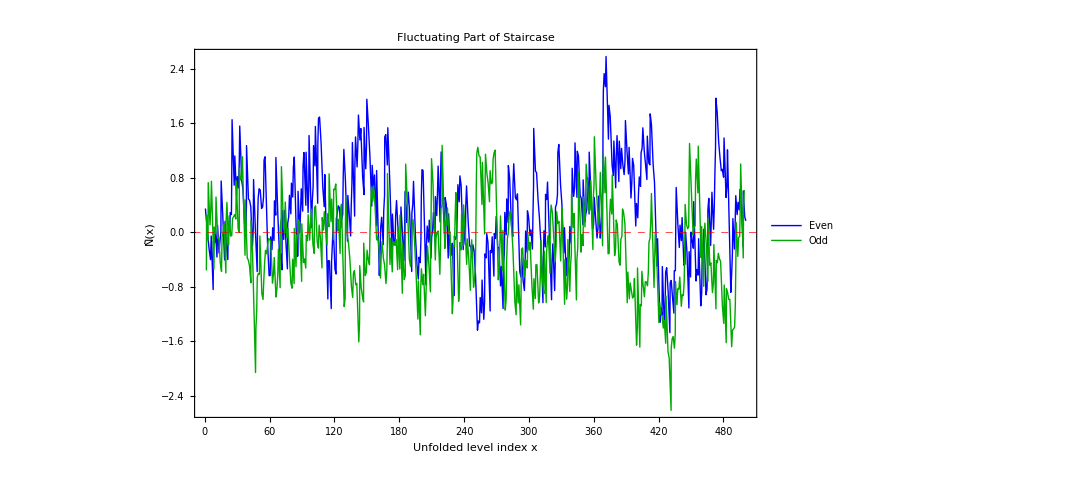

```mathematica
(*---Fluctuating staircase---*)
Legended[Show[ListLinePlot[Transpose[{flucEven["x"],flucEven["delta"]}],PlotStyle->{Blue,AbsoluteThickness[1]}],ListLinePlot[Transpose[{flucOdd["x"],flucOdd["delta"]}],PlotStyle->{Darker[Green],AbsoluteThickness[1]}],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"Unfolded level index x","\!\(\*OverscriptBox[\(N\), \(~\)]\)(x)"},PlotLabel->"Fluctuating Part of Staircase",GridLines->{None,{0}},GridLinesStyle->Directive[Red,Dashed],PlotRange->All],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[1]],Directive[Darker[Green],AbsoluteThickness[1]]},{"Even","Odd"},LabelStyle->Directive[Black,18]],{Right,Bottom}]]
```

```mathematica
(*Length spectrum:FT of fluctuating density*)
LengthSpectrum[fluc_Association]:=Module[{n,ft,periods},n=fluc["N"];
ft=Fourier[fluc["delta"],FourierParameters->{1,-1}];
periods=Range[0,n-1]/n;(*in units of Heisenberg time*)
<|"Period"->periods[[1;;Floor[n/2]]],"Amplitude"->Re[ft[[1;;Floor[n/2]]]]|>];
```

```mathematica
lsEven=LengthSpectrum[flucEven];
lsOdd=LengthSpectrum[flucOdd];
```

```mathematica
Legended[Show[ListLinePlot[Transpose[{lsEven["Period"],lsEven["Amplitude"]}],PlotStyle->{Blue,AbsoluteThickness[1]}],ListLinePlot[Transpose[{lsOdd["Period"],lsOdd["Amplitude"]}],PlotStyle->{Red,AbsoluteThickness[1]}],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"τ (Heisenberg time units)","Length Spectrum"},PlotLabel->"Length Spectrum: J="<>ToString[J]<>", k="<>ToString[N[k]],GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->All],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[1]],Directive[Red,AbsoluteThickness[1]]},{"Even","Odd"},LabelStyle->Directive[Black,18]],{Right,Bottom}]]
```

```mathematica
(*Zoom into short orbits:first 50 kick periods*)nShow=50;
Legended[Show[ListLinePlot[Transpose[{lsEven["Period"][[1;;nShow]],lsEven["Amplitude"][[1;;nShow]]}],PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotMarkers->Automatic],ListLinePlot[Transpose[{lsOdd["Period"][[1;;nShow]],lsOdd["Amplitude"][[1;;nShow]]}],PlotStyle->{Red,AbsoluteThickness[1.5]},PlotMarkers->Automatic],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"Period (kicks)","Length Spectrum"},PlotLabel->"Short Orbit Region",GridLines->{Range[50],{0}},GridLinesStyle->Directive[Gray,Dashed,Opacity[0.3]],PlotRange->All],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[1.5]],Directive[Red,AbsoluteThickness[1.5]]},{"Even","Odd"},LabelStyle->Directive[Black,18]],{Right,Bottom}]]
```

```mathematica
LengthSpectrumWindowed[fluc_Association,sigma_:0.1]:=Module[{n,nHalf,x,window,ft,periods},n=fluc["N"];
nHalf=Floor[n/2];
x=Range[n]/n;
window=Exp[-(x-0.5)^2/(2 sigma^2)];
ft=Fourier[fluc["delta"]*window,FourierParameters->{1,-1}];
periods=Range[0,nHalf-1];
<|"Period"->periods,"Amplitude"->Re[ft[[1;;nHalf]]]|>];
```

```mathematica
lsEven=LengthSpectrumWindowed[flucEven];
lsOdd=LengthSpectrumWindowed[flucOdd];
```

```mathematica
Legended[Show[ListLinePlot[Transpose[{lsEven["Period"],lsEven["Amplitude"]}],PlotStyle->{Blue,AbsoluteThickness[1]}],ListLinePlot[Transpose[{lsOdd["Period"],lsOdd["Amplitude"]}],PlotStyle->{Red,AbsoluteThickness[1]}],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"τ (Heisenberg time units)","Length Spectrum"},PlotLabel->"Length Spectrum: J="<>ToString[J]<>", k="<>ToString[N[k]],GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->All],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[1]],Directive[Red,AbsoluteThickness[1]]},{"Even","Odd"},LabelStyle->Directive[Black,18]],{Right,Bottom}]]
```

```mathematica
(*Zoom into short orbits:first 50 kick periods*)nShow=50;
Legended[Show[ListLinePlot[Transpose[{lsEven["Period"][[1;;nShow]],lsEven["Amplitude"][[1;;nShow]]}],PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotMarkers->Automatic],ListLinePlot[Transpose[{lsOdd["Period"][[1;;nShow]],lsOdd["Amplitude"][[1;;nShow]]}],PlotStyle->{Red,AbsoluteThickness[1.5]},PlotMarkers->Automatic],Frame->True,ImageSize->800,FrameStyle->Directive[30,Black],LabelStyle->Directive[30,Black],FrameLabel->{"Period (kicks)","Length Spectrum"},PlotLabel->"Short Orbit Region",GridLines->{Range[50],{0}},GridLinesStyle->Directive[Gray,Dashed,Opacity[0.3]],PlotRange->All],Placed[LineLegend[{Directive[Blue,AbsoluteThickness[1.5]],Directive[Red,AbsoluteThickness[1.5]]},{"Even","Odd"},LabelStyle->Directive[Black,18]],{Right,Bottom}]]
```

# Eigenvectors

## Eigenvectors

```mathematica
radius=2;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31397,2}

```mathematica
(*Floquet parameters*)
J=513;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"];
```

Generating coherent states over 31397 points...

```mathematica
rot=MatrixExp[I(α/2)ops[[3]]];
```

```mathematica
α=Pi/2.;
k=13.7;
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
(*mat=ConjugateTranspose[rot].Floq[J,α,k].rot;*)
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
{rM,rm}={MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.547664,0.418804}

```mathematica
(rM-0.38)/(0.53-0.38)
(rm-0.38)/(0.53-0.38)
```

1.11776

0.258694

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```